# ICCS Clone

## Parameters

```mathematica
(*Constants*)
mc2=0.511*10^6; (*electron mass eV/c^2*)
me=9.11*10^-31; (*electron mass kg*)
c=299792458; (*SI*)
r0=2.8179403262*10^-15; (*SI*)
echarge=1.60217662*10^-19; (*SI*)
ϵ0=8.8541878128*10^-12; (*SI*)
hbar=6.5821*10^-16; (*in eV s*)
kg2eVc2=5.36*10^-28;
```

```mathematica
(*Source Parameters*)
θa=0.435*10^-3; (*semiangle of collimator - our collimation angle*)
τ=10*10^-12; (*pulse duraction of laser*)
λ=1064*10^-9;
Epulse=62*10^-6;
f=325*10^6;
σL=25*10^-6;
```

## Electron Bunch Momentum Distribution

When a tracked distribution is not available: 
 p_i=pδ(0,1)√ϵ_i/β_i 
can be used to create a distribution where δ(0,1) is a Gaussian distributed random variable with zero mean and unit variance, i=x,y,z.

```mathematica
(*Need to pull the distribution into an array here, where we can easily select px,py,pz*)
```

```mathematica
momdist=Import["C:/Users/user/Documents/Wolfram Mathematica/Bmad_ICCS_data/mom_dat_0.5%.txt","Words"];
```

```mathematica
Npart=Length[momdist]/3;
```

```mathematica
(*Creation of Data Array*)
momdata=Array[m,{3,Npart}];
```

```mathematica
For[i=1,i<(Npart+1),i++,
(*px*)
momdata⟦1,i⟧=Interpreter["Number"][ToString[momdist⟦1+3*(i-1)⟧]];
(*py*)
momdata⟦2,i⟧=Interpreter["Number"][ToString[momdist⟦2+3*(i-1)⟧]];
(*pz*)
momdata⟦3,i⟧=Interpreter["Number"][ToString[momdist⟦3+3*(i-1)⟧]];
];
```

## Electron Beam Momentum Distribution

```mathematica
momdist=Partition[{momdata⟦1,All⟧,momdata⟦2,All⟧,momdata⟦3,All⟧}~Flatten~{2,1},3];
```

```mathematica
ListPointPlot3D[momdist,PlotLabel->"Electron Beam Momentum Distribution",AxesLabel->{"p_x (kgms^-1)","p_y (kgms^-1)","p_z (kgms^-1)"}]
```

-Graphics3D-

## Intermediaries

cθ is cosθ, sθ is sinθ, cosθ and sinθ are used this way as integral is over cosθ. px, py, pz are the momentum values of a particular particle.

```mathematica
pbar[px_,py_,pz_]:=Sqrt[px^2+py^2+pz^2];
γ[px_,py_,pz_]:=Sqrt[1+(pbar[px,py,pz]/(me*c))^2];
β[px_,py_,pz_]:=pbar[px,py,pz]/(γ[px,py,pz]*me*c);
sθ[cθ_]:=Sqrt[1-cθ^2];
σ[τ_,λ_]:=(τ*c)/λ;
a0[λ_,Epulse_,f_,σL_]:=0.85*10^-9*(λ*10^6)*Sqrt[(Epulse*f)/(2*π*(σL*10^2)^2)];
```

## Electron Energy Distribution

```mathematica
Eevspart=Table[Sqrt[(1/kg2eVc2*pbar[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧])^2+mc2^2]*10^-6,{i,1,Npart}];
```

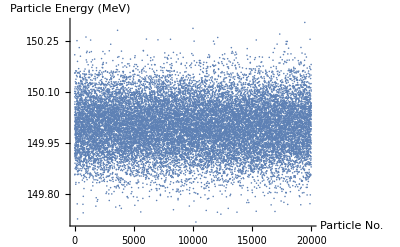

```mathematica
ListPlot[Eevspart,AxesLabel->{"Particle No.","Particle Energy (MeV)"}]
```

## Scattered Photon Energy

```mathematica
EL[λ_]:=(2*π*hbar*c)/λ;
Xrec[px_,py_,pz_]:=(4*γ[px,py,pz]*EL[λ])/mc2;
```

```mathematica
(*Head-on case only implemented, uses cos^-1 as integral performed for cosθ*)
Eγ[px_,py_,pz_,λ_,cθ_]:=(4*γ[px,py,pz]^2*EL[λ])/(1+γ[px,py,pz]^2*ArcCos[cθ]^2+Xrec[px,py,pz]);
```

```mathematica
Eγ[momdata⟦1,23⟧,momdata⟦2,23⟧,momdata⟦3,23⟧,λ,1]
```

402386.

## Laser Angular Frequency + Frame Change

```mathematica
ω[px_,py_,pz_,λ_,cθ_,ϕ_]:=(Eγ[px,py,pz,λ,cθ]/hbar*(1-β[px,py,pz]/pbar[px,py,pz]*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]*Sin[ϕ]+pz*cθ)))/(1+(β[px,py,pz]*pz)/pbar[px,py,pz]-Eγ[px,py,pz,λ,cθ]/(γ[px,py,pz]*mc2)*(1+cθ));
```

```mathematica
dω[px_,py_,pz_,λ_,cθ_,ϕ_]:=(1+β[px,py,pz]/pbar[px,py,pz]*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]*Sin[ϕ]+pz*cθ)-(β[px,py,pz]^2*pz)/pbar[px,py,pz]^2*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]+pz*cθ))/(1+(β[px,py,pz]*pz)/pbar[px,py,pz]-Eγ[px,py,pz,λ,cθ]/(γ[px,py,pz]*mc2)*(1+cθ));
```

## Laser Angular Frequency Plots

```mathematica
ωvspart=Table[ω[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
(*Wavenumber x speed of light, as in ω - kc term in expontential of electric field, to do with the dispersion relation*)
kc=Table[(2*π*c)/λ,{i,1,Npart}];
```

```mathematica
ListPlot[{ωvspart,kc},PlotRange->Full,PlotLabel->"Effective Angular Frequency of Laser Photon Acting on Each Particle" ,AxesLabel->{"Particle No.", "Effective Laser Angular Frequency (Hz)"}]
```

-Graphics-

```mathematica
ELvspart=Table[hbar*ω[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
kcEL=Table[hbar*(2*π*c)/λ,{i,1,Npart}];
```

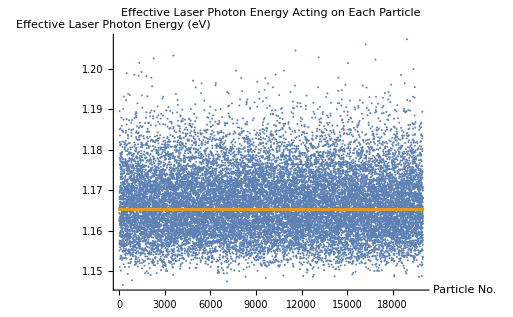

```mathematica
ListPlot[{ELvspart,kcEL},PlotRange->Full,PlotLabel->"Effective Laser Photon Energy Acting on Each Particle" ,AxesLabel->{"Particle No.", "Effective Laser Photon Energy (eV)"}]
```

## Electric Field Terms

```mathematica
(*Prefactor*)
Elecprefac[λ_,Epulse_,f_,σL_,τ_]:=(a0[λ,Epulse,f,σL]*c*me*σ[τ,λ]*λ)/echarge^2*Sqrt[π/2];
```

```mathematica
(*Exponential Term 1 Logarithm*)
arg1[px_,py_,pz_,λ_,cθ_,ϕ_,τ_]:=(-(σ[τ,λ]*λ)^2)/(2*c^2)*(ω[px,py,pz,λ,cθ,ϕ]-(2*π*c)/λ)^2;
```

```mathematica
(*First Exponential term*)
expterm1[px_,py_,pz_,λ_,cθ_,ϕ_,τ_]:=Exp[(-(σ[τ,λ]*λ)^2)/(2*c^2)*(ω[px,py,pz,λ,cθ,ϕ]-(2*π*c)/λ)^2];
```

```mathematica
(*Exponential Term 2 Logarithm*)
```

```mathematica
arg2[px_,py_,pz_,λ_,cθ_,ϕ_,τ_]:=(-4*π*σ[τ,λ]^2*λ*ω[px,py,pz,λ,cθ,ϕ])/c;
```

```mathematica
(*Second Exponential term*)
```

```mathematica
expterm2[px_,py_,pz_,λ_,cθ_,ϕ_,τ_]:=Chop[Exp[(-4*π*σ[τ,λ]^2*λ*ω[px,py,pz,λ,cθ,ϕ])/c]]+1;
```

```mathematica
(*Implemented a chop within this funtion for when σ is small i.e we have a very small exponential part*)
```

## Electric Field Term Plots

```mathematica
(*Plots of the first exponential term of the Electric field, at inside (Subscript[θ, a]=0) and outside (Subscript[θ, a]=Subscript[θ, col]) of collimator*)
```

```mathematica
exp1partθa=Table[expterm1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0,τ],{i,1,Npart}];
```

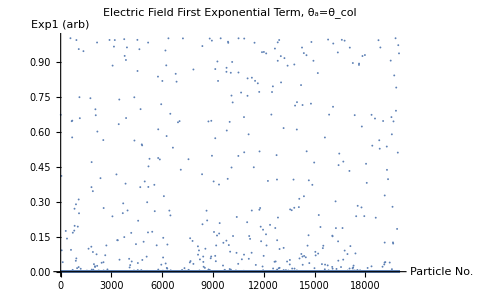

```mathematica
ListPlot[exp1partθa,PlotRange->Full,PlotLabel->"Electric Field First Exponential Term, θ_a=θ_col",AxesLabel->{"Particle No.","Exp1 (arb)"}]
```

```mathematica
exp1part0=Table[expterm1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0,τ],{i,1,Npart}];
```

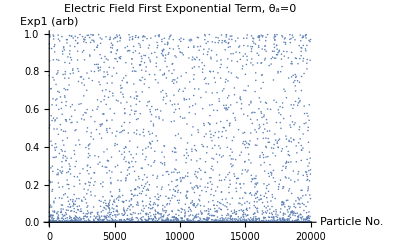

```mathematica
ListPlot[exp1part0,PlotRange->Full,PlotLabel->"Electric Field First Exponential Term, θ_a=0",AxesLabel->{"Particle No.","Exp1 (arb)"}]
```

```mathematica
(*Plots of the second exponential term (and it's argument) of the Electric field, at inside (Subscript[θ, a]=0) and outside (Subscript[θ, a]=Subscript[θ, col]) of collimator*)
```

```mathematica
arg2partθa=Table[arg2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0,τ],{i,1,Npart}];
```

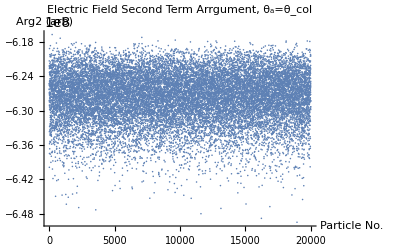

```mathematica
ListPlot[arg2partθa,PlotRange->Full,PlotLabel->"Electric Field Second Term Arrgument, θ_a=θ_col",AxesLabel->{"Particle No.","Arg2 (arb)"}]
```

```mathematica
exp2partθa=Table[expterm2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0,τ],{i,1,Npart}];
```

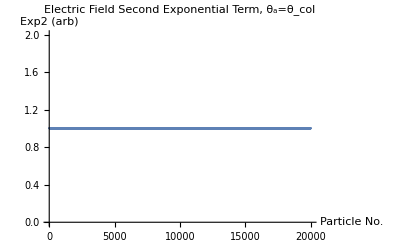

```mathematica
ListPlot[exp2partθa,PlotLabel->"Electric Field Second Exponential Term, θ_a=θ_col",AxesLabel->{"Particle No.","Exp2 (arb)"}]
```

```mathematica
arg2part0=Table[arg2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0,τ],{i,1,Npart}];
```

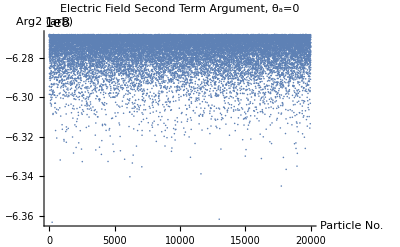

```mathematica
ListPlot[arg2part0,PlotRange->Full,PlotLabel->"Electric Field Second Term Argument, θ_a=0",AxesLabel->{"Particle No.","Arg2 (arb)"}]
```

```mathematica
exp2part0=Table[expterm2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0,τ],{i,1,Npart}];
```

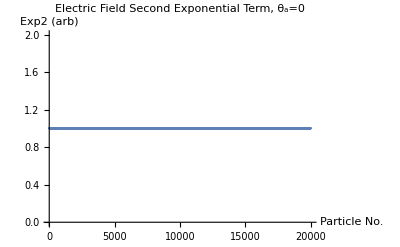

```mathematica
ListPlot[exp2part0,PlotLabel->"Electric Field Second Exponential Term, θ_a=0",AxesLabel->{"Particle No.","Exp2 (arb)"}]
```

## Electric Field

```mathematica
Elec[px_,py_,pz_,cθ_,ϕ_,Epulse_,f_,σL_,τ_,λ_]:=Elecprefac[λ,Epulse,f,σL,τ]*ω[px,py,pz,λ,cθ,ϕ]*expterm1[px,py,pz,λ,cθ,ϕ,τ]*expterm2[px,py,pz,λ,cθ,ϕ,τ];
```

```mathematica
Elecvspart=Table[Elec[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],0,Epulse,f,σL,τ,λ],{i,1,Npart}];
```

```mathematica
ListPlot[Elecvspart,PlotRange->Full,PlotLabel->"Electric Field Operating on Each Particle",AxesLabel->{"Particle No.", "Electric Field (Vm^-1)"}]
```

-Graphics-

## Interaction Cross Section Terms

```mathematica
(*Term 0*)
X0[px_,py_,pz_,λ_,cθ_,ϕ_]:=((1+cθ-(Eγ[px,py,pz,λ,cθ]/(γ[px,py,pz]*mc2)*(1+cθ)))/(1-β[px,py,px]/pbar[px,py,pz]*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]*Sin[ϕ]+pz*cθ)))^2;
```

```mathematica
(*Term 1*) 
X1[px_,py_,pz_,λ_,cθ_]:=(1+cθ-((Eγ[px,py,pz,λ,cθ]/(γ[px,py,pz]*mc2))*(1+cθ)))/(1+β[px,py,pz]);
```

```mathematica
(*Term 2*)
X2[px_,py_,pz_,cθ_,ϕ_]:=(2*(me*sθ[cθ]*Cos[ϕ])^2)/(γ[px,py,pz]*me-1/c*(px*sθ[cθ]*Cos[ϕ]+py*sθ[cθ]*Sin[ϕ]+pz*cθ))^2;
```

```mathematica
(*Term 3*)
X3[px_,py_,pz_,cθ_,ϕ_]:=((2*me)^2*c*px*sθ[cθ]*(1+cθ)*Cos[ϕ])/((γ[px,py,pz]*me+pz/c)*(γ[px,py,pz]*me*c-px*sθ[cθ]*Cos[ϕ]-py*sθ[cθ]*Sin[ϕ]-pz*cθ)^2);
```

```mathematica
(*Term 4*)
X4[px_,py_,pz_,cθ_,ϕ_]:=(2*(me*px*(1+cθ))^2)/((γ[px,py,pz]*me*c+pz/c)*(γ[px,py,pz]*me*c-px*sθ[cθ]*Cos[ϕ]-py*sθ[cθ]*Sin[ϕ]-pz*cθ))^2;
```

```mathematica
(*Cross Section Terms*)
```

```mathematica
DSXterms[px_,py_,pz_,λ_,cθ_,ϕ_]:=X0[px,py,pz,λ,cθ,ϕ]*(X1[px,py,pz,λ,cθ]+1/X1[px,py,pz,λ,cθ]-X2[px,py,pz,cθ,ϕ]+X3[px,py,pz,cθ,ϕ]-X4[px,py,pz,cθ,ϕ]);
```

## Interaction Cross Section Term Plots

```mathematica
(*Term 0 Plots*)
```

```mathematica
X0θa=Table[X0[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
X01=Table[X0[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,1⟧,λ,1,0],{i,1,Npart}];
```

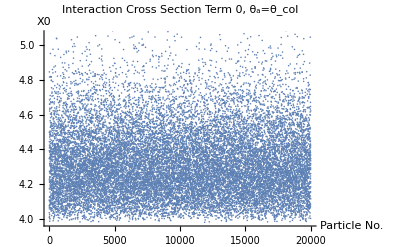

```mathematica
ListPlot[X0θa,PlotLabel-> "Interaction Cross Section Term 0, θ_a=θ_col", AxesLabel->{"Particle No.","X0"}]
```

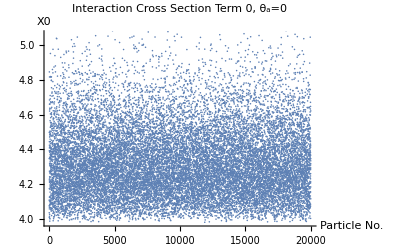

```mathematica
ListPlot[X01,PlotLabel-> "Interaction Cross Section Term 0, θ_a=0", AxesLabel->{"Particle No.","X0"}]
```

```mathematica
(*Term 1 Plot*)
```

```mathematica
X1θa=Table[X1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa]],{i,1,Npart}];
```

```mathematica
X10=Table[X1[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1],{i,1,Npart}];
```

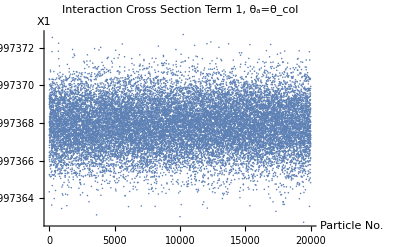

```mathematica
ListPlot[X1θa,PlotLabel-> "Interaction Cross Section Term 1, θ_a=θ_col", AxesLabel->{"Particle No.","X1"}]
```

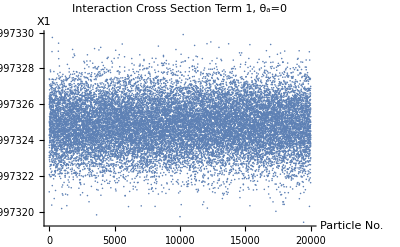

```mathematica
ListPlot[X10,PlotLabel-> "Interaction Cross Section Term 1, θ_a=0", AxesLabel->{"Particle No.","X1"}]
```

```mathematica
(*Term 2 Plot*)
```

```mathematica
X2θa=Table[X2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],0],{i,1,Npart}];
```

```mathematica
X20=Table[X2[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,1,0],{i,1,Npart}];
```

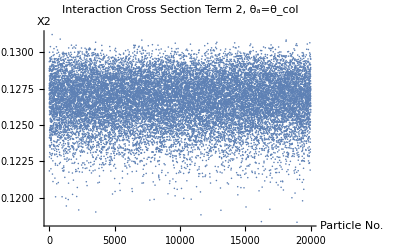

```mathematica
ListPlot[X2θa,PlotLabel-> "Interaction Cross Section Term 2, θ_a=θ_col", AxesLabel->{"Particle No.","X2"}]
```

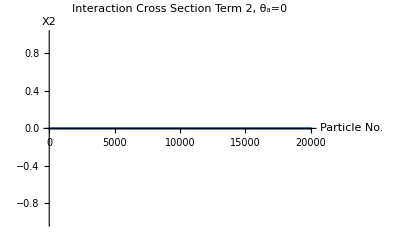

```mathematica
ListPlot[X20,PlotLabel-> "Interaction Cross Section Term 2, θ_a=0", AxesLabel->{"Particle No.","X2"}]
```

Expected that X20 has zero values as sθ reliance in numerator.

```mathematica
(*Term 3 Plots*)
```

```mathematica
X3θa=Table[X3[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],0],{i,1,Npart}];
```

```mathematica
X30=Table[X3[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,1,0],{i,1,Npart}];
```

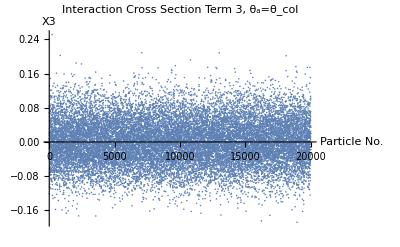

```mathematica
ListPlot[X3θa,PlotLabel-> "Interaction Cross Section Term 3, θ_a=θ_col", AxesLabel->{"Particle No.","X3"}]
```

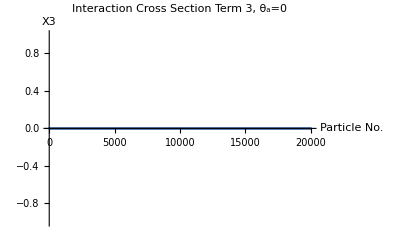

```mathematica
ListPlot[X30,PlotLabel-> "Interaction Cross Section Term 3, θ_a=0", AxesLabel->{"Particle No.","X3"}]
```

sinθ term in the numerator means that X30 should be zero for this case.

```mathematica
(*Term 4 Plots*)
```

```mathematica
X4θa=Table[X4[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],0],{i,1,Npart}];
```

```mathematica
X40=Table[X4[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,1,0],{i,1,Npart}];
```

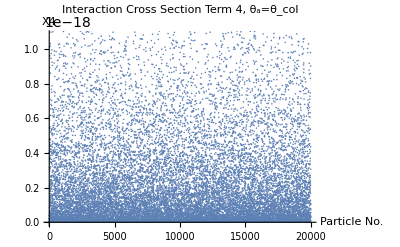

```mathematica
ListPlot[X4θa,PlotLabel-> "Interaction Cross Section Term 4, θ_a=θ_col", AxesLabel->{"Particle No.","X4"}]
```

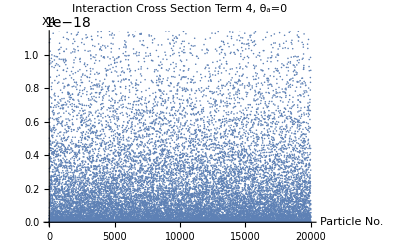

```mathematica
ListPlot[X40,PlotLabel-> "Interaction Cross Section Term 4, θ_a=0", AxesLabel->{"Particle No.","X4"}]
```

```mathematica
(*Terms Together Plots*)
```

```mathematica
Termsθa=Table[DSXterms[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
Terms0=Table[DSXterms[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0],{i,1,Npart}];
```

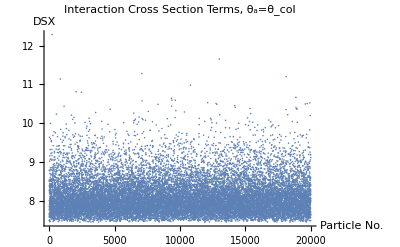

```mathematica
ListPlot[Termsθa,PlotRange->Full,PlotLabel-> "Interaction Cross Section Terms, θ_a=θ_col", AxesLabel->{"Particle No.","DSX"}]
```

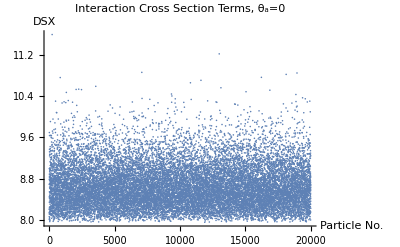

```mathematica
ListPlot[Terms0,PlotRange->Full,PlotRange->Full,PlotLabel-> "Interaction Cross Section Terms, θ_a=0", AxesLabel->{"Particle No.","DSX"}]
```

## Interaction Cross Section Calculation

```mathematica
dσdΩ[px_,py_,pz_,λ_,cθ_,ϕ_]:=1/2*(r0/(γ[px,py,pz]*(1+β[px,py,pz])))^2*DSXterms[px,py,pz,λ,cθ,ϕ];
```

## Interaction Cross Section Plots

```mathematica
dσdΩθa=Table[dσdΩ[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,Cos[θa],0],{i,1,Npart}];
```

```mathematica
dσdΩ0=Table[dσdΩ[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,λ,1,0],{i,1,Npart}];
```

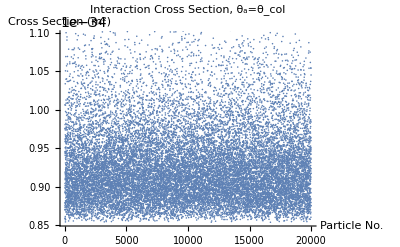

```mathematica
ListPlot[dσdΩθa,PlotLabel->"Interaction Cross Section, θ_a=θ_col",AxesLabel->{"Particle No.","Cross Section (m^2)"}]
```

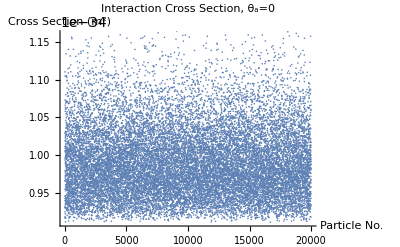

```mathematica
ListPlot[dσdΩ0,PlotLabel->"Interaction Cross Section, θ_a=0",AxesLabel->{"Particle No.","Cross Section (m^2)"}]
```

This is much lower than we would expect right? The expected value would be on the order of the Thomson Cross Section σ_T= 6.65 x10^-29 m^2.

## Energy Spectra Single Particle

```mathematica
SPprefac=(ϵ0*c)/(2*π);
```

```mathematica
SPintterm[px_,py_,pz_,cθ_,ϕ_,Epulse_,f_,σL_,τ_,λ_]:=Chop[Abs[Elec[px,py,pz,cθ,ϕ,Epulse,f,σL,τ,λ]^2]*dσdΩ[px,py,pz,λ,cθ,ϕ]*(Eγ[px,py,pz,λ,cθ]/hbar)/ω[px,py,pz,λ,cθ,ϕ]*dω[px,py,pz,λ,cθ,ϕ]];
```

```mathematica
singpart0=Table[SPintterm[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,1,π,Epulse,f,σL,τ,λ],{i,1,Npart}];
```

```mathematica
ListPlot[singpart0,PlotRange->All]
```

-Graphics-

```mathematica
singpartθa=Table[SPintterm[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],π,Epulse,f,σL,τ,λ],{i,1,Npart}];
```

```mathematica
ListPlot[singpartθa,PlotRange->All]
```

-Graphics-

```mathematica
(*Integral over ϕ, 0 to 2π*)
```

```mathematica
SPINTterm[px_,py_,pz_,cθ_,Epulse_,f_,σL_,τ_,λ_]:=NIntegrate[SPintterm[px,py,pz,cθ,ϕ,Epulse,f,σL,τ,λ],{ϕ,0,2*π}];
```

```mathematica
intsingpart0=Table[SPINTterm[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,1,Epulse,f,σL,τ,λ],{i,1,Npart}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
ListPlot[intsingpart0,PlotRange->Full]
```

-Graphics-

```mathematica
SPINTterm[momdata⟦1,1⟧,momdata⟦2,1⟧,momdata⟦3,1⟧,Cos[θa],Epulse,f,σL,τ,λ]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
intsingpartθa=Table[SPINTterm[momdata⟦1,i⟧,momdata⟦2,i⟧,momdata⟦3,i⟧,Cos[θa],Epulse,f,σL,τ,λ],{i,1,Npart}];
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
Plot[SPINTterm[momdata⟦1,10000⟧,momdata⟦2,10000⟧,momdata⟦3,10000⟧,cθ,Epulse,f,σL,τ,λ],{cθ,Cos[θa],1}]
```

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]